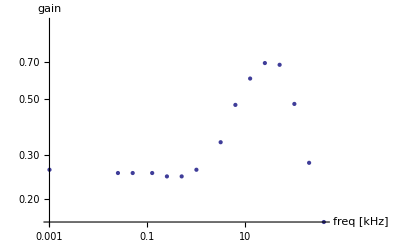

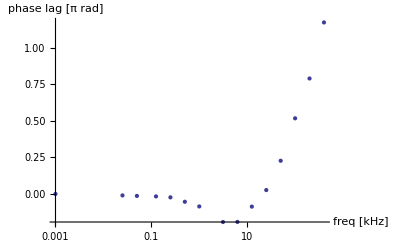

```mathematica
f={200 10^3,100 10^3,400 10^3,50 10^3,25 10^3, 12.5 10^3,6.25 10^3,3.125 10^3,1 10^3,500,250,125,50,25,1};
H={156/560,400/840,52/320,272/400,304/440,264/440,472/1000,336/1000,272/1040,256/1040,256/1040,264/1040,264/1040,264/1040,272/1040};
mag=Thread[{f 10^-3,H}];

Δt={1.974,2.586,1.466,2.27,.532,-3.46,-15.3,-30.7,-42.7,-53.4,-46.6,-66.8,-134,-200,0} 10^-6;
phase=Thread[{f 10^-3,2 f Δt}];

ListLogLogPlot[mag,AxesLabel->{"freq [kHz]","gain"}]
ListLogLinearPlot[phase,AxesLabel->{"freq [kHz]","phase lag [π rad]"}]
```